字符串模式与模板

字符串模式的工作原理与 Wolfram 语言中的其他模式非常相似，只是它们对字符串中的字符序列而不是表达式的一部分进行操作。在一个字符串模式中，你可以使用 ~~ 将如 _ 等模式结构与 "abc" 等字符串结合起来。

这将取出所有 + 后面跟着一个字符的实例：

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~_]
```

{+s,+p,+q,+e}

这就取出 + 后面的三个字符：

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~_~~_~~_]
```

{+str,+pat,+qui,+eas}

将每个 + 后面的字符使用 x 的名字，并返回该字符加上边框。

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~x_->Framed[x]]
```

{s,p,q,e}

在字符串模式中， _ 可表示任何单个字符。_ _ (“double blank”)可表示任何一个或多个字符的序列，而 _ _ _ (“triple blank”)可表示任何零个或多个字符的序列。_ _ 和 _ _ _ 通常会尽可能多地抓取字符串的内容。

取出 [ 和 ] 之间的字符序列：

```mathematica
StringCases["the [important] word", "["~~x__~~"]"->Framed[x]]
```

{important}

_ _ 通常会匹配尽可能长的字符序列：

```mathematica
StringCases["now [several] important [words]", "["~~x__~~"]"->Framed[x]]
```

{several] important [words}

Shortest 将使其强制进行最短的匹配：

```mathematica
StringCases["now [several] important [words]", "["~~Shortest[x__]~~"]"->Framed[x]]
```

{several,words}

StringCases 在一个字符串中取出特定模式的情况。StringReplace 则是进行替换。

对字符串中的字符进行替换：

```mathematica
StringReplace["now [several] important [words]", {"["->"<<","]"->">>"}]
```

now <<several>> important <<words>>

对模式进行替换，在每种情况下使用 :> 来计算 ToUpperCase。
Make replacements for patterns, using :> to compute ToUpperCase in each case:

```mathematica
StringReplace["now [several] important [words]", "["~~Shortest[x__]~~"]":>ToUpperCase[x]]
```

now SEVERAL important WORDS

使用 NestList 来重复应用字符串替换：

```mathematica
NestList[StringReplace[#,{"A"->"AB","B"->"BA"}]&,"A",5]
```

{A,AB,ABBA,ABBABAAB,ABBABAABBAABABBA,ABBABAABBAABABBABAABABBAABBABAAB}

StringMatchQ 用于测试一个字符串是否与一个模式相匹配。

选择匹配以 a 开头、以 b 结尾的模式的常用词：

```mathematica
Select[WordList[ ],StringMatchQ[#,"a"~~___~~"b"]&]
```

{absorb,adsorb,adverb,alb,aplomb}

你可以在字符串模式中使用 | and ..，就像在普通模式中一样。

取出任何重复的 A 或 B 的序列：

```mathematica
StringCases["the AAA and the BBB and the ABABBBABABABA",("A"|"B")..]
```

{AAA,BBB,ABABBBABABABA}

在字符串模式中，LetterCharacter 表示任何字母字符，DigitCharacter 表示任何数字字符，Whitespace 表示代表任何“空白”字符的序列，比如空格。

取出数字字符的序列：

```mathematica
StringCases["12 and 123 and 4567 and 0x456",DigitCharacter..]
```

{12,123,4567,0,456}

取出被空白字符“包围”的数字字符序列：

```mathematica
StringCases["12 and 123 and 4567 and 0x456",Whitespace~~DigitCharacter..~~Whitespace]
```

{ 123 , 4567 }

在实际中，想要在字符串和列表之间来回切换是很常见的。你可以使用 StringSplit 来将一个字符串分割成一个列表。

将一个字符串分割成一个列表，默认在空格处断开：

```mathematica
StringSplit["a string to split"]
```

{a,string,to,split}

使用一个字符串模式来决定分割的位置：

```mathematica
StringSplit["you+can+split--at+any--delimiter","+"|"--"]
```

{you,can,split,at,any,delimiter}

在字符串中，有一个特殊的换行符，表示字符串应该在哪里换行。换行符在字符串中被表示为 \n。

在新行处分割：

```mathematica
StringSplit["first line
second line
third line","\n"]
```

{first line,second line,third line}

StringJoin 用于将任何字符串列表连接在一起。但在实践中，人们经常希望在连接字符串之前在它们之间插入一些东西。StringRiffle 可以做到这一点。

连接字符串，在它们之间插入字符串 "---"。

```mathematica
StringRiffle[{"a","list","of","strings"},"---"]
```

a---list---of---strings

在连接字符串时，人们经常想把任意的 Wolfram 语言表达式转换为字符串。我们可以用 TextString 来做这件事。

TextString 用于将数字和其他 Wolfram 语言表达式转换为字符串。

```mathematica
StringJoin["two to the ",TextString[50]," is ",TextString[2^50]]
```

two to the 50 is 1125899906842624

从表达式创建字符串的一个更方便的方法是使用字符串模板。字符串模板的工作方式与纯函数类似，它们有可以插入参数的槽。

在字符串模板中，每个 `` 都是一个连续参数的槽：

```mathematica
StringTemplate["first `` then ``"][100,200]
```

first 100 then 200

命名的槽将从一个关联中取出元素：

```mathematica
StringTemplate["first: `a`; second `b`; first again `a`"][<|"a"->"AAAA", "b"->"BB BBB"|>]
```

first: AAAA; second BB BBB; first again AAAA

你可以通过用 <*...*> 括起来以在字符串模板中插入任何表达式。当模板被应用时，将会计算表达式的值。

在应用模板时计算 <*...*>；不需要参数：

```mathematica
StringTemplate["2 to the 50 is <* 2^50 *>"][ ]
```

2 to the 50 is 1125899906842624

在模板中使用槽(` 是反引号符)。

```mathematica
StringTemplate["`1` to the `2` is <* #1^#2 *>"][2,50]
```

2 to the 50 is 1125899906842624

模板中的表达式在应用模板时进行计算：

```mathematica
StringTemplate["the time now is <* Now *>"][ ]
```

the time now is Wed 16 Sep 2015 16:50:43

词汇

patt_1~~patt_2 |   | 字符串模式序列
Shortest[patt] |   | 匹配到的最短序列
StringCases[string,patt] |   | 字符串中与模式匹配的情况
StringReplace[string,patt→val] |   | 替换字符串中的模式
StringMatchQ[string,patt] |   | 测试一个字符串是否与一个模式相匹配
LetterCharacter |   | 匹配字母的模式
DigitCharacter |   | 匹配数字的模式
Whitespace |   | 匹配空白字符的模式
\n |   | 换行符
StringSplit[string] |   | 将字符串分割为片段列表
StringJoin[{string_1,string_2, ...}] |   | 将字符串进行连接
StringRiffle[{string_1,string_2, ...},m] |   | 连接字符串，并在字符串之间插入 m
TextString[expr] |   | 使用任何东西来创建字符串
StringTemplate[string] |   | 创建一个字符串模板
`` |   | 字符串模板中的槽
<*...*> |   | 在字符串模板中进行计算的表达式

"共有 8 道习题" | "开始练习 »"

将 "1 2 3 4" 中的每个空格替换为 "---"。»

| 期望输出： |  
  | "1---2---3---4" |

获取维基百科上关于计算机的词条中所有 4 位数的序列(代表可能的日期)的排序列表。»

| 期望输出示例： |  
  | {"1000","1235","1357","1357","1500","1595","1613","1620","1630","1770","1833","1872","1872","1876","1876","1888","1901","1906","1920","1927","1930","1931","1934","1936","1936","1938","1939","1941","1942","1943","1943","1943","1944","1945","1945","1945","1945","1947","1947","1947","1948","1950","1950","1951","1951","1952","1953","1953","1955","1955","1955","1957","1958","1958","1959","1970","1970","1990","2000","2000","2013","2400","2400","2468","4004","5000"} |

提取维基百科上关于计算机的词条中的 “标题”，它是由以 "===" 开头和结尾的字符串表示的。»

| 期望输出示例： |  
  | {" Pre-twentieth century "," First general-purpose computing device "," Later Analog computers "," Digital computer development ","= Electromechanical ","= Vacuum tubes and digital electronic circuits ","= Stored programs ","= Transistors ","= Integrated circuits "," Mobile computers become dominant "," Stored program architecture "," Machine code "," Programming language ","= Low-level languages ","= High-level languages/Third Generation Language "," Fourth Generation Languages "," Program design "," Bugs "," Control unit "," Central Processing unit (CPU) "," Arithmetic logic unit (ALU) "," Memory "," Input/output (I/O) "," Multitasking "," Multiprocessing "," Computer architecture paradigms "," Unconventional computing "," Artificial intelligence "," History of computing hardware "," Other hardware topics "," Firmware "," Liveware "," Based on uses "," Based on sizes "} |

使用字符串模板来创建一个 i+j=... 形式的结果网格，其中 i 和 j 最大为 9。(加法口诀表)»

| 期望输出： |  
  | "1+1=2" | "1+2=3" | "1+3=4" | "1+4=5" | "1+5=6" | "1+6=7" | "1+7=8" | "1+8=9" | "1+9=10"
"2+1=3" | "2+2=4" | "2+3=5" | "2+4=6" | "2+5=7" | "2+6=8" | "2+7=9" | "2+8=10" | "2+9=11"
"3+1=4" | "3+2=5" | "3+3=6" | "3+4=7" | "3+5=8" | "3+6=9" | "3+7=10" | "3+8=11" | "3+9=12"
"4+1=5" | "4+2=6" | "4+3=7" | "4+4=8" | "4+5=9" | "4+6=10" | "4+7=11" | "4+8=12" | "4+9=13"
"5+1=6" | "5+2=7" | "5+3=8" | "5+4=9" | "5+5=10" | "5+6=11" | "5+7=12" | "5+8=13" | "5+9=14"
"6+1=7" | "6+2=8" | "6+3=9" | "6+4=10" | "6+5=11" | "6+6=12" | "6+7=13" | "6+8=14" | "6+9=15"
"7+1=8" | "7+2=9" | "7+3=10" | "7+4=11" | "7+5=12" | "7+6=13" | "7+7=14" | "7+8=15" | "7+9=16"
"8+1=9" | "8+2=10" | "8+3=11" | "8+4=12" | "8+5=13" | "8+6=14" | "8+7=15" | "8+8=16" | "8+9=17"
"9+1=10" | "9+2=11" | "9+3=12" | "9+4=13" | "9+5=14" | "9+6=15" | "9+7=16" | "9+8=17" | "9+9=18" |

在 50 以下的整数的名称中，找出在 “e” 之前的某个位置有 “i” 的那些。»

| 期望输出： |  
  | {"five","nine","thirteen","fifteen","sixteen","eighteen","nineteen","twenty-five","twenty-nine","thirty-one","thirty-three","thirty-five","thirty-seven","thirty-eight","thirty-nine","forty-five","forty-nine"} |

在维基百科上关于计算机的文章的第一句话中，将所有双字母的单词大写。»

| 期望输出示例： |  
  | "A computer IS a general-purpose device that can BE programmed TO carry out a set OF arithmetic OR logical operations automatically." |

将所有国家按 TextString 名称的首字母进行分组，然后创建一个有标签的条形图。»

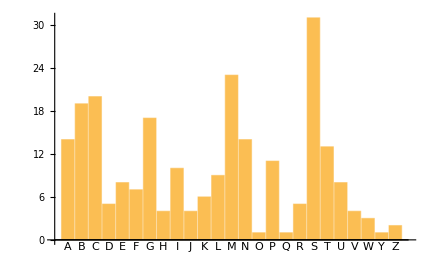
| 期望输出： |  
  | -Graphics- |

为 Grid[Table[StringJoin[TextString[i],"^",TextString[j],"=",TextString[i^j]],{i,5},{j,5}]] 找到更简单的形式。»

| 期望输出： |  
  | "1^1=1" | "1^2=1" | "1^3=1" | "1^4=1" | "1^5=1"
"2^1=2" | "2^2=4" | "2^3=8" | "2^4=16" | "2^5=32"
"3^1=3" | "3^2=9" | "3^3=27" | "3^4=81" | "3^5=243"
"4^1=4" | "4^2=16" | "4^3=64" | "4^4=256" | "4^5=1024"
"5^1=5" | "5^2=25" | "5^3=125" | "5^4=625" | "5^5=3125" |

问&答

如何读 ~~？

通常读作“波浪号波浪号”。底层函数是 StringExpression。

如何在字符串模板中输入 `` 来创建一个槽？

它是一对通常被称为反引号的字符。在许多键盘上，它们与~(波浪号)一起位于键盘的左上方。

我可以为理解自然语言编写规则吗？

是的，但我们在这里并没有涉及。关键的函数是 GrammarRules。

当对象没有明显的文本形式时，TextString 会做什么？

它尽力创建一些人类可读的东西，但如果所有其他方法都失败了，它就会退回到 InputForm。

技术笔记

字符串的模式和列表中的序列模式之间有一种对应关系。SequenceCases 是字符串的 StringCases 在列表方面的相似函数。

选项 Overlaps 指定了在字符串匹配中是否允许重叠。不同的函数有不同的默认值。

字符串模式默认匹配最长的序列，所以如果你想要最短序列，需要指定 Shortest。表达式模式默认匹配最短序列。

在字符串模式结构中，有 Whitespace、NumberString、WordBoundary、StartOfLine、EndOfLine、StartOfString 以及 EndOfString。

在 Wolfram 语言符号字符串模式的任何地方，你都可以使用 RegularExpression 来包括正则表达式语法，比如 x* 和 [abc][def]。

TextString 会尝试从任何给定对象来创建一个简单的人类可读的文本版本，放弃了像图像细节这样的东西。ToString[InputForm[expr]] 将给出一个完整的版本，适合后续输入。

你可以使用 SequenceAlignment 等操作来比较字符串。这在生物信息学中特别有用。

FileTemplate、XMLTemplate 以及 NotebookTemplate 让你可以对文件、XML(和 HTML)文档以及笔记本做类似 StringTemplate 的工作。

Wolfram 语言中包括 TextSearch 函数，用于从大量文件集合中搜索文本。

探索更多

Wolfram 语言中的字符串模式 »